### List of points

```mathematica
r1 = Range[-4,6,2];
r2 = Range[4,-6,-2];
pos = Transpose[{ r1,r2}]
```

{{-4,4},{-2,2},{0,0},{2,-2},{4,-4},{6,-6}}

```mathematica
pos = Append[Transpose[{r2, r1}], pos]
```

{{4,-4},{2,-2},{0,0},{-2,2},{-4,4},{-6,6},{{-4,4},{-2,2},{0,0},{2,-2},{4,-4},{6,-6}}}

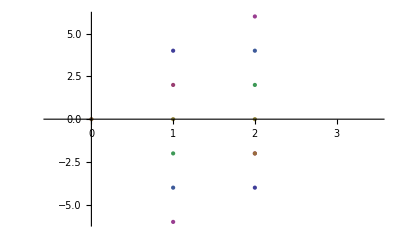

```mathematica
ListPlot[pos]
```

```mathematica
colors = {{87, 93, 94}, {77, 73, 78}, {30, 
  30, 37}, {137, 143, 134}, {115, 115, 106}, {86, 93, 
  80}}
```

{{87,93,94},{77,73,78},{30,30,37},{137,143,134},{115,115,106},{86,93,80}}

```mathematica
stuff = Transpose[{pos, colors}]
```

{{{-4,4},{87,93,94}},{{-2,2},{77,73,78}},{{0,0},{30,30,37}},{{2,-2},{137,143,134}},{{4,-4},{115,115,106}},{{6,-6},{86,93,80}}}

```mathematica
stuff[[1,1,1]] (*This is how to access the first element of the list*)
```

```mathematica
-4
```

```mathematica
Table[{x[t]/.First[relPoints[pos[[f]],c,m,force,3]], p[t]/.First[relPoints[pos[[f]],c,m,force,10]]} ,{f,1,20}]
```

```mathematica
(*puts point into ndsolve *)
```

```mathematica
dv[{point_, c_, m_, f_, tf_}] := {x[t]/.First[relPoints[pos[[point]],c,m,force,3]], p[t]/.First[relPoints[pos[[point]],c,m,force,10]]}
```

```mathematica
dp[{point_, c_, m_, f_, tf_}] := {x[t]/.First[relPoints[pos[[point]],c,m,force,3]], p[t]/.First[relPoints[pos[[point]],c,m,force,10]]}
```

```mathematica
f[{p_, c_}]:={{p[[1]]+dv[p, c, m , f, tf]*dt, p[[2]]+dp[p, c, m, f, tf]*dt}, c}
```

```mathematica
relPoints = Function[{a,c,m, f,tf},NDSolve[{p'[t]==f[x[t]], x'[t]==(p[t]/m)/Sqrt[1+(p[t]/(m*c))^2],x[0]==a[[1]],p[0]==a[[2]]},{x,p},{t,0,tf}]];
(*Newtonian*)
newtPoints = Function[{a,c,m, f,tf},NDSolve[{p'[t]==f[x[t]], x'[t]==p[t]/m,x[0]==a[[1]],p[0]==a[[2]]},{x,p},{t,0,tf}]];
hookef[x_]:= -4x;
cf[x_]:=1;
sinf[x_]:=Sin[x];
tanf[x_]:=-Tan[x];
```

```mathematica
Map[f, stuff]
```

Part::partd: Part specification (-4) ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification (-4) ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification (-2) ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{{{{87 dv[-4,4,m,f,tf]+(-4)⟦1⟧,93 dv[-4,4,m,f,tf]+(-4)⟦1⟧,94 dv[-4,4,m,f,tf]+(-4)⟦1⟧},{87 dp[-4,4,m,f,tf]+(-4)⟦2⟧,93 dp[-4,4,m,f,tf]+(-4)⟦2⟧,94 dp[-4,4,m,f,tf]+(-4)⟦2⟧}},4},{{{77 dv[-2,2,m,f,tf]+(-2)⟦1⟧,73 dv[-2,2,m,f,tf]+(-2)⟦1⟧,78 dv[-2,2,m,f,tf]+(-2)⟦1⟧},{77 dp[-2,2,m,f,tf]+(-2)⟦2⟧,73 dp[-2,2,m,f,tf]+(-2)⟦2⟧,78 dp[-2,2,m,f,tf]+(-2)⟦2⟧}},2},{{{30 dv[0,0,m,f,tf]+0⟦1⟧,30 dv[0,0,m,f,tf]+0⟦1⟧,37 dv[0,0,m,f,tf]+0⟦1⟧},{30 dp[0,0,m,f,tf]+0⟦2⟧,30 dp[0,0,m,f,tf]+0⟦2⟧,37 dp[0,0,m,f,tf]+0⟦2⟧}},0},{{{137 dv[2,-2,m,f,tf]+2⟦1⟧,143 dv[2,-2,m,f,tf]+2⟦1⟧,134 dv[2,-2,m,f,tf]+2⟦1⟧},{137 dp[2,-2,m,f,tf]+2⟦2⟧,143 dp[2,-2,m,f,tf]+2⟦2⟧,134 dp[2,-2,m,f,tf]+2⟦2⟧}},-2},{{{115 dv[4,-4,m,f,tf]+4⟦1⟧,115 dv[4,-4,m,f,tf]+4⟦1⟧,106 dv[4,-4,m,f,tf]+4⟦1⟧},{115 dp[4,-4,m,f,tf]+4⟦2⟧,115 dp[4,-4,m,f,tf]+4⟦2⟧,106 dp[4,-4,m,f,tf]+4⟦2⟧}},-4},{{{86 dv[6,-6,m,f,tf]+6⟦1⟧,93 dv[6,-6,m,f,tf]+6⟦1⟧,80 dv[6,-6,m,f,tf]+6⟦1⟧},{86 dp[6,-6,m,f,tf]+6⟦2⟧,93 dp[6,-6,m,f,tf]+6⟦2⟧,80 dp[6,-6,m,f,tf]+6⟦2⟧}},-6}}

## Todo : Make a list of points (different initial conditions) Give each point a color Make a function which evolves the points Draw the evolution

Todo:a conditions different initial list Make of points

a color each Give point

a evolves function Make points the which

Draw evolution the

```mathematica
Rasterize[-Graphics-, RasterSize->{3,2}]
```

-Graphics-

```mathematica
InputForm[%]
```

Null

```mathematica
Graphics[Raster[{{{87, 93, 94}, {77, 73, 78}, {30, 
  30, 37}}, {{137, 143, 134}, {115, 115, 106}, {86, 93, 
  80}}}, {{0, 0}, {30.857142857142854, 
    123.42857142857142}}, {0, 255}, 
  ColorFunction -> RGBColor]]
```

-Graphics-

```mathematica
(*Create 20 random points, pair the numbers using transpose. Rerun to get a new set of points.*)
r1 = RandomReal[{-4,4},{1000}];
r2 = RandomReal[{-4,4},{1000}];
pos = Transpose[{ r1,r2}];
```

```mathematica
(*Different force functions*)
hookef[x_]:= -4x;
cf[x_]:=1;
sinf[x_]:=Sin[x];
tanf[x_]:=-Tan[x];
```

```mathematica
NewtEvolvePoints = Function[{l,f,m, dt,t},{l[[1]]+(l[[2]]/m)*dt, l[[2]]+f[l[[1]]]*dt}];
```

```mathematica
NewtEvolveManyPoints = Function[{l},{l[[1]]+(l[[2]]/1)*.1, l[[2]]+Sin[l[[1]]]*.1}];
```

```mathematica
Map[NewtEvolveManyPoints,pos];
```

```mathematica
pos0 = pos;
```

```mathematica
p0 = {1,0};
```

```mathematica
(*Multiple points*)
```

```mathematica
Animate[pos0=Map[NewtEvolveManyPoints,pos0];
	StreamPlot[{v,Sin[x]},{x,-5,5},{v,-5,5},
			Epilog->{Red,PointSize->Large,Point[
			pos0
			], PlotRange->{{-5,5},{-5,5}} ,AspectRatio->1}]
		       ,{t,0,4/2Pi},AnimationRunning->True
	      ]
```

```mathematica
(*One point*)
```

```mathematica
Animate[If[t≠0,p0=NewtEvolvePoints[p0,sinf,1,.1,t]];
	StreamPlot[{v,Sin[x]},{x,-5,5},{v,-5,5},
			Epilog->{Red,PointSize->Large,Point[
			{p0}
			], PlotRange->{{-5,5},{-5,5}} ,AspectRatio->1}]
		       ,{t,0,4/2Pi},AnimationRunning->True
	      ]
```